## Объявление глобальных переменных

```mathematica
print@x_:=(Print@x;x);
```

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["/Users/kirillivanov/Documents/Code/For Geant analysis/log_final.csv"];
data//TableForm
```

№ | Absorber | Gap | a | sigma a | b | sigma b
1 | Plumbum | Neon | 0.00515412 | 0.00158296 | 5.48892 | 0.0833476
2 | Plumbum | Argon | 0.00559905 | 0.00173068 | 6.13976 | 0.0910907
3 | Plumbum | Xeon | 0.00876149 | 0.00175214 | 6.81182 | 0.0919066
4 | Ferrum | Neon | 0.00852034 | 0.00216812 | 6.63051 | 0.114281
5 | Ferrum | Argon | 0.00738885 | 0.00211958 | 7.22538 | 0.111433
6 | Ferrum | Xeon | 0.00909037 | 0.00152497 | 7.00896 | 0.080146
7 | Wolfram | Neon | 0.00283894 | 0.00138977 | 5.61903 | 0.0730131
8 | Wolfram | Argon | 0.00748688 | 0.000725038 | 6.01597 | 0.0381172
9 | Wolfram | Xeon | 0.0075177 | 0.00209043 | 6.86425 | 0.109846

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00692864]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00692864 | 0.00067781 | 10.2221 | 7.2026×10^-6

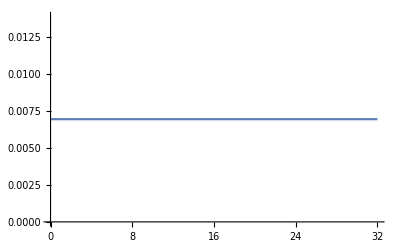

```mathematica
forFit=data⟦2;;,{1,4}⟧;
forFitCr=data⟦2;;,5⟧;
fit=LinearModelFit[forFit,{1},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit["FitResiduals"])/(print@forFitCr))^2
```

{-0.00177452,-0.00132959,0.00183285,0.0015917,0.000460217,0.00216174,-0.0040897,0.00055824,0.000589059}

{0.00158296,0.00173068,0.00175214,0.00216812,0.00211958,0.00152497,0.00138977,0.000725038,0.00209043}

{1.25667,0.590203,1.09426,0.538959,0.0471439,2.00947,8.65962,0.592817,0.0794051}

```mathematica
χ2=Total[(fit["FitResiduals"]/forFitCr)^2]/(9-1)
```

1.85857

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

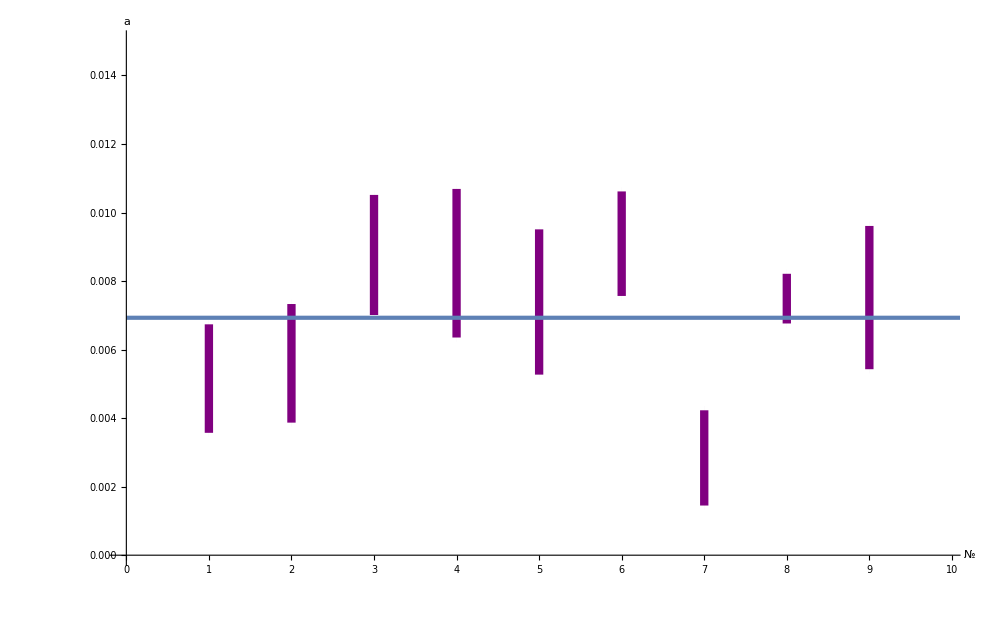

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/final_a.png

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/final_res_a.png

```mathematica
plot =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,1,5}⟧,
GridLines->{grids@1,grids@0.001},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"№","a"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)(*,
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX,Automatic},
PlotRange->{{0,9.9},{0,0.015}}], 
Plot[fit["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/final_a.png",plot,"PNG"]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/final_res_a.png",fit@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportA = {fit@"BestFitParameters",fit@"ParameterErrors", χ2}
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_final_a.csv",exportA,"CSV"]
```

{{0.00692864},{0.00067781},1.85857}

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_final_a.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["/Users/kirillivanov/Documents/Code/For Geant analysis/log_final.csv"];
data//TableForm
```

№ | Absorber | Gap | a | sigma a | b | sigma b
1 | Plumbum | Neon | 0.00515412 | 0.00158296 | 5.48892 | 0.0833476
2 | Plumbum | Argon | 0.00559905 | 0.00173068 | 6.13976 | 0.0910907
3 | Plumbum | Xeon | 0.00876149 | 0.00175214 | 6.81182 | 0.0919066
4 | Ferrum | Neon | 0.00852034 | 0.00216812 | 6.63051 | 0.114281
5 | Ferrum | Argon | 0.00738885 | 0.00211958 | 7.22538 | 0.111433
6 | Ferrum | Xeon | 0.00909037 | 0.00152497 | 7.00896 | 0.080146
7 | Wolfram | Neon | 0.00283894 | 0.00138977 | 5.61903 | 0.0730131
8 | Wolfram | Argon | 0.00748688 | 0.000725038 | 6.01597 | 0.0381172
9 | Wolfram | Xeon | 0.0075177 | 0.00209043 | 6.86425 | 0.109846

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[6.42273]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 6.42273 | 0.208862 | 30.751 | 1.35884×10^-9

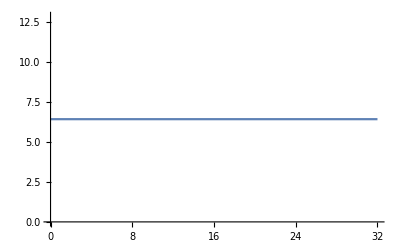

```mathematica
forFitb=data⟦2;;,{1,6}⟧;
forFitCrb=data⟦2;;,7⟧;
fitb=LinearModelFit[forFitb,{1},x]
fitb@"ParameterTable"
Plot[fitb["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fitb["FitResiduals"])/(print@forFitCrb))^2
```

{-0.933815,-0.282977,0.389086,0.207781,0.802651,0.586228,-0.803705,-0.406761,0.441512}

{0.0833476,0.0910907,0.0919066,0.114281,0.111433,0.080146,0.0730131,0.0381172,0.109846}

{125.526,9.6506,17.9224,3.30573,51.8833,53.5019,121.169,113.877,16.1554}

```mathematica
χ2b=Total[(fitb["FitResiduals"]/forFitCrb)^2]/(9-1)
```

64.1241

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

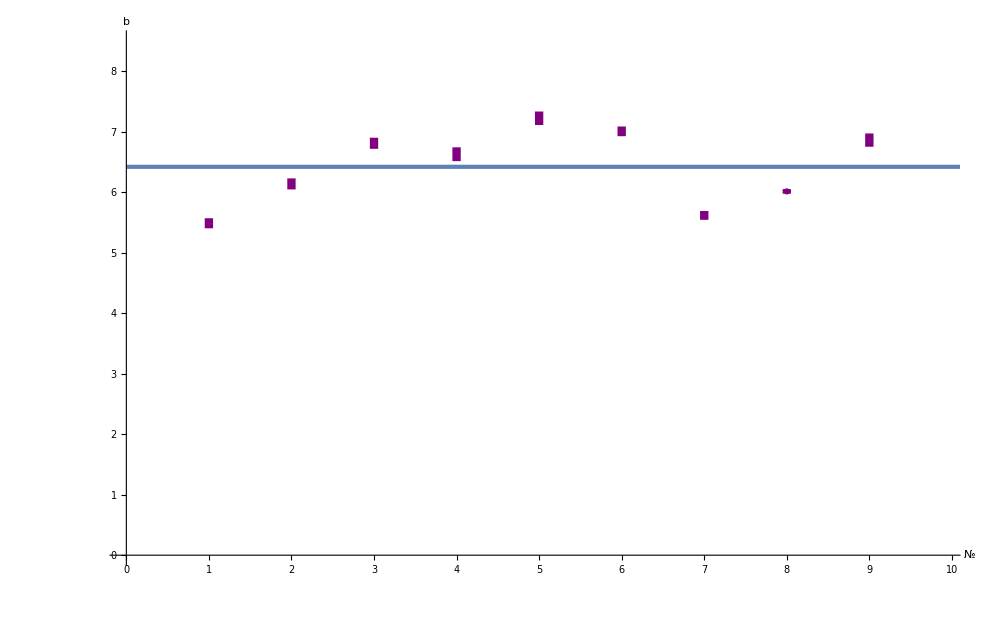

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/final_b.png

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/final_res_b.png

```mathematica
plotb=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,6,1,7}⟧,
GridLines->{grids@1,grids@1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"№","b"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)(*,
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX,Automatic},
PlotRange->{{0,9.9},{0,8.5}}], 
Plot[fitb["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/final_b.png",plotb,"PNG"]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/final_res_b.png",fitb@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportB = {fitb@"BestFitParameters",fitb@"ParameterErrors", χ2b}
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_final_b.csv",exportB,"CSV"]
```

{{6.42273},{0.208862},64.1241}

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_final_b.csv